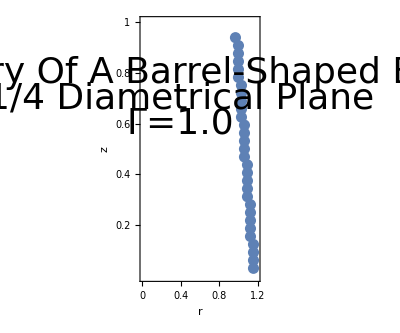

```mathematica
F={{1.156250,0.031250},{1.156250,0.062500},{1.156250,0.093750},{1.156250,0.125000},{1.125000,0.156250},{1.125000,0.187500},{1.125000,0.218750},{1.125000,0.250000},{1.125000,0.281250},{1.093750,0.312500},{1.093750,0.343750},{1.093750,0.375000},{1.093750,0.406250},{1.093750,0.437500},{1.062500,0.468750},{1.062500,0.500000},{1.062500,0.531250},{1.062500,0.562500},{1.062500,0.593750},{1.031250,0.625000},{1.031250,0.656250},{1.031250,0.687500},{1.031250,0.718750},{1.031250,0.750000},{1.000000,0.781250},{1.000000,0.812500},{1.000000,0.843750},{1.000000,0.875000},{1.000000,0.906250},{0.968750,0.937500}};
ListPlot[F,PlotStyle->PointSize[0.02],Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,0.2,0.4,0.6,0.8,1,1.2},None}}, PlotRange->{{0,1.2},{0,1}},FrameLabel->{{"z", None},{"r", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],Epilog->{Text[Style["Boundary Of A Barrel-Shaped Bridge",Directive[Black,36]],{0.4,0.8}],Text[Style["1/4 Diametrical Plane",Directive[Black,36]],{0.4,0.7}],Text[Style["Γ=1.0",Directive[Black,36]],{0.4,0.6}]},AspectRatio->5/6]
```

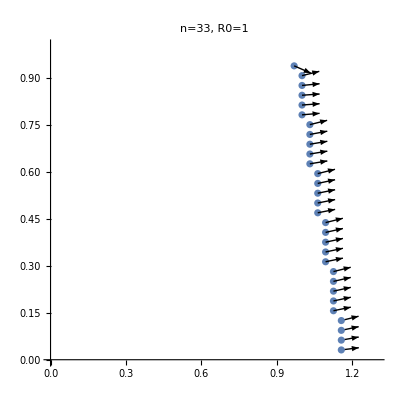

```mathematica
FF={Arrow[{{1.156250,0.031250},{1.225893,0.038312}}],Arrow[{{1.156250,0.062500},{1.225537,0.072466}}],Arrow[{{1.156250,0.093750},{1.225267,0.105440}}],Arrow[{{1.156250,0.125000},{1.224891,0.138728}}],Arrow[{{1.125000,0.156250},{1.194057,0.167702}}],Arrow[{{1.125000,0.187500},{1.193990,0.199347}}],Arrow[{{1.125000,0.218750},{1.193933,0.230923}}],Arrow[{{1.125000,0.250000},{1.193849,0.262640}}],Arrow[{{1.125000,0.281250},{1.193641,0.294978}}],Arrow[{{1.093750,0.312500},{1.162778,0.324122}}],Arrow[{{1.093750,0.343750},{1.162754,0.355515}}],Arrow[{{1.093750,0.375000},{1.162721,0.386961}}],Arrow[{{1.093750,0.406250},{1.162640,0.418666}}],Arrow[{{1.093750,0.437500},{1.162391,0.451228}}],Arrow[{{1.062500,0.468750},{1.131657,0.479583}}],Arrow[{{1.062500,0.500000},{1.131640,0.510937}}],Arrow[{{1.062500,0.531250},{1.131606,0.542399}}],Arrow[{{1.062500,0.562500},{1.131503,0.574275}}],Arrow[{{1.062500,0.593750},{1.131141,0.607478}}],Arrow[{{1.031250,0.625000},{1.100652,0.634131}}],Arrow[{{1.031250,0.656250},{1.100646,0.665422}}],Arrow[{{1.031250,0.687500},{1.100616,0.696901}}],Arrow[{{1.031250,0.718750},{1.100479,0.729112}}],Arrow[{{1.031250,0.750000},{1.099891,0.763728}}],Arrow[{{1.000000,0.781250},{1.069837,0.786027}}],Arrow[{{1.000000,0.812500},{1.069872,0.816724}}],Arrow[{{1.000000,0.843750},{1.069888,0.847712}}],Arrow[{{1.000000,0.875000},{1.069788,0.880443}}],Arrow[{{1.000000,0.906250},{1.068641,0.919978}}],Arrow[{{0.968750,0.937500},{1.034837,0.914425}}]};
ListPlot[F, Epilog->{FF},PlotRange->{{0,1.3},{0,1}},AspectRatio->1/1, PlotLabel->"n=33, R0=1"]
```

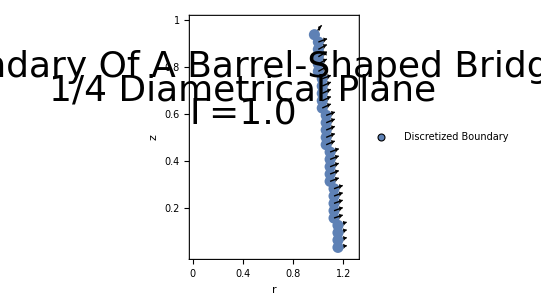

```mathematica
FF2={Arrow[{{1.156250,0.031250},{1.225880,0.038442}}],Arrow[{{1.156250,0.062500},{1.225503,0.072696}}],Arrow[{{1.156250,0.093750},{1.225225,0.105683}}],Arrow[{{1.156250,0.125000},{1.224891,0.138728}}],Arrow[{{1.125000,0.156250},{1.193881,0.168719}}],Arrow[{{1.125000,0.187500},{1.193787,0.200477}}],Arrow[{{1.125000,0.218750},{1.193720,0.232076}}],Arrow[{{1.125000,0.250000},{1.193671,0.263574}}],Arrow[{{1.125000,0.281250},{1.193641,0.294978}}],Arrow[{{1.093750,0.312500},{1.162310,0.326624}}],Arrow[{{1.093750,0.343750},{1.162274,0.358048}}],Arrow[{{1.093750,0.375000},{1.162257,0.389382}}],Arrow[{{1.093750,0.406250},{1.162275,0.420542}}],Arrow[{{1.093750,0.437500},{1.162391,0.451228}}],Arrow[{{1.062500,0.468750},{1.130789,0.484133}}],Arrow[{{1.062500,0.500000},{1.130776,0.515438}}],Arrow[{{1.062500,0.531250},{1.130788,0.546639}}],Arrow[{{1.062500,0.562500},{1.130867,0.577532}}],Arrow[{{1.062500,0.593750},{1.131141,0.607478}}],Arrow[{{1.031250,0.625000},{1.099153,0.642006}}],Arrow[{{1.031250,0.656250},{1.099144,0.673291}}],Arrow[{{1.031250,0.687500},{1.099174,0.704421}}],Arrow[{{1.031250,0.718750},{1.099340,0.734992}}],Arrow[{{1.031250,0.750000},{1.099891,0.763728}}],Arrow[{{1.000000,0.781250},{1.066948,0.801695}}],Arrow[{{1.000000,0.812500},{1.066812,0.833385}}],Arrow[{{1.000000,0.843750},{1.066744,0.864852}}],Arrow[{{1.000000,0.875000},{1.067077,0.895017}}],Arrow[{{1.000000,0.906250},{1.068641,0.919978}}],Arrow[{{0.968750,0.937500},{1.026069,0.977681}}]};
q1=ListPlot[F, Epilog->{FF2,Text[Style["Boundary Of A Barrel-Shaped Bridge",Directive[Black,36]],{0.4,0.8}],Text[Style["1/4 Diametrical Plane",Directive[Black,36]],{0.4,0.7}],Text[Style["Γ=1.0",Directive[Black,36]],{0.4,0.6}]},PlotStyle->PointSize[0.02],Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,0.2,0.4,0.6,0.8,1,1.2},None}}, PlotRange->{{0,1.3},{0,1}},FrameLabel->{{"z", None},{"r", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],AspectRatio->10/13,PlotLegends->Placed[PointLegend[{"Discretized Boundary"},LegendMarkers->{{Graphics[Disk[]],25}}],{Left, Bottom}]]
```

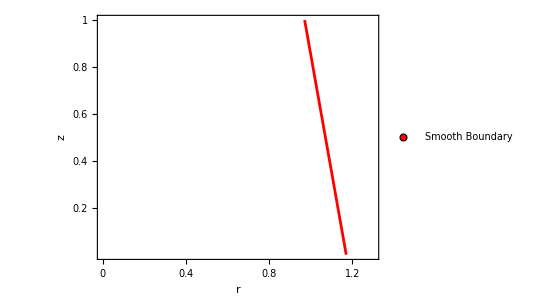

```mathematica
q2=Plot[y=5.85-5 x,{x,0.97,1.17}, Frame->{True, True, True, True}, PlotStyle->{Red, Thickness[0.005]},FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,0.2,0.4,0.6,0.8,1,1.2},None}}, PlotRange->{{0,1.3},{0,1}},FrameLabel->{{"z", None},{"r", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->{Thickness[0.005]},LabelStyle->Directive[Black,36],AspectRatio->10/13,PlotLegends->Placed[PointLegend[{"Smooth Boundary"},LegendMarkers->{{Graphics[Disk[]],25}}],{Left, Bottom}]]
```

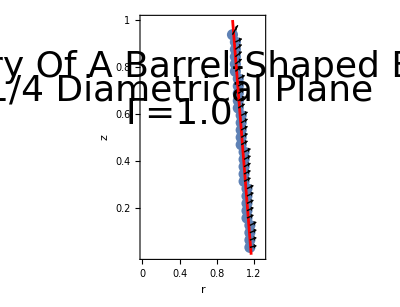

```mathematica
Show[q1,q2]
```